# Digital Research Methods 02A: Text Search

## William J Turkel, wturkel@uwo.ca History 2816 / Digital Humanities 2130 / History 9877

## Overview

By studying word frequencies, we can get an idea of the importance of various terms in our texts, whether they are common or uncommon. Once we have identified some terms of interest, we need methods that allow us to search our text(s) to discover how those terms are used.

## Setup

Last class we loaded a ResourceObject containing the ‘State of the Union’ addresses of US Presidents, and used word frequency analysis to study two speeches that President Harry S. Truman made in January of 1946 and 1950, respectively. Here are the commands that we used to retrieve each text, count the words in each, and determine the most frequent non-stopwords.

```mathematica
stateOfTheUnion=First[ResourceSearch["state of the union"]];
```

```mathematica
hstJan1946String=Get[stateOfTheUnion]⟦157⟧["Text"];
```

```mathematica
hstJan1946FrequencyAssociation=WordCounts[hstJan1946String,IgnoreCase->True];
```

```mathematica
hstJan1946FrequentTerms=DeleteStopwords[Keys[hstJan1946FrequencyAssociation⟦1;;100⟧]]
```

```mathematica
hstJan1950String=Get[stateOfTheUnion]⟦161⟧["Text"];
```

```mathematica
hstJan1950FrequencyAssociation=WordCounts[hstJan1950String,IgnoreCase->True];
```

```mathematica
hstJan1950FrequentTerms=DeleteStopwords[Keys[hstJan1950FrequencyAssociation⟦1;;100⟧]];
```

We are also going to create two new lists. These contain all of the word types that are used in a particular speech, not including stopwords

```mathematica
hstJan1946Terms=DeleteStopwords[Keys[hstJan1946FrequencyAssociation]];
```

```mathematica
hstJan1950Terms=DeleteStopwords[Keys[hstJan1950FrequencyAssociation]];
```

## Word clouds

In Mathematica, we can use the WordCloud command to create a display which scales each word in a text according to its frequency. Here we begin with the string containing the text of the speech, DeleteStopwords, and then create the word cloud.

### January 1946

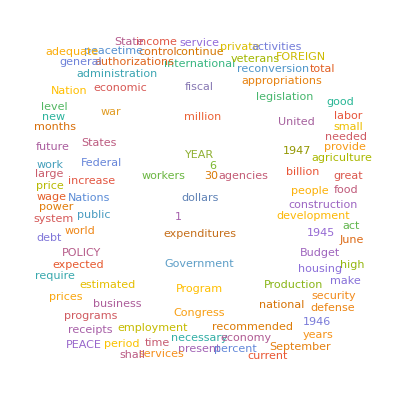

```mathematica
WordCloud[DeleteStopwords[hstJan1946String]]
```

### January 1950

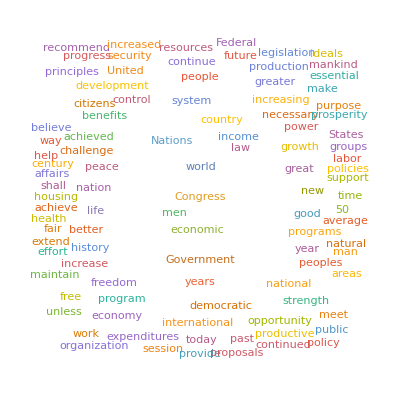

```mathematica
WordCloud[DeleteStopwords[hstJan1950String]]
```

## Searching through a list of sentences

When we look at a word cloud, we can see the relative importance of a particular term, but we don’t have any sense of the context in which it is used. Suppose, for example, we want to know how the word ‘peacetime’ was used in Truman’s 1946 speech.

The TextSentences command breaks a string into a list of sentences.

```mathematica
hstJan1946Sentences=TextSentences[hstJan1946String];
```

```mathematica
Head[hstJan1946Sentences]
```

List

Here is the first sentence of the speech

```mathematica
First[hstJan1946Sentences]
```

To the Congress of the United States:  
A quarter century ago the Congress decided that it could no longer consider the financial programs of the various departments on a piecemeal basis.

### StringContainsQ

To test whether one string contains another, we can use the StringContainsQ command.

Here is the first sentence

```mathematica
hstJan1946Sentences⟦1⟧
```

To the Congress of the United States:  
A quarter century ago the Congress decided that it could no longer consider the financial programs of the various departments on a piecemeal basis.

Does the first sentence contain the word “piecemeal”?

```mathematica
StringContainsQ[hstJan1946Sentences⟦1⟧,"piecemeal"]
```

True

Does the first sentence contain the word “peacetime”?

```mathematica
StringContainsQ[hstJan1946Sentences⟦1⟧,"peacetime"]
```

False

### Select, with an anonymous function

What we really want is a list of all of the sentences in the 1946 speech which contain the word “peacetime”. To get this list, we use the Select command. We have to tell Select what we are looking for, and to do this, we are going to use an anonymous function based on StringContainsQ. We will learn more about anonymous functions throughout the course.

The anonymous function looks like this

StringContainsQ[#, "peacetime"] &

Here is how we apply the function to an argument

```mathematica
(StringContainsQ[#,"peacetime"]&)["this is a test"]
```

False

```mathematica
(StringContainsQ[#,"peacetime"]&)["this sentence contains the word peacetime"]
```

True

Here is how we use our anonymous function to Select all of the sentences that contain the word “peacetime”

```mathematica
Select[hstJan1946Sentences,StringContainsQ[#,"peacetime"]&]
```

{Since our programs for this period which combines war liquidation with reconversion to a peacetime economy are inevitably large and numerous it is imperative that they be planned and executed with the utmost efficiency and the utmost economy.,We have held our peacetime programs to the level necessary to our national well-being and the attainment of our postwar objectives.,We face a great peacetime venture; the challenging venture of a free enterprise economy making full and effective use of its rich resources and technical advances.,Labor also has its own new peacetime responsibilities.,Their transition to peacetime pursuits will be determined by our efforts to break the bottlenecks in key items of production, to make surplus property immediately available where it is needed, to maintain an effective national employment service, and many other reconversion policies.,While our peacetime prosperity will be based on the private enterprise the government can and must assist in many ways.,For example, the establishment of new peacetime industries in the Western States and in the South would, in my judgment, add to existing production and markets rather than merely bring about a shifting of production.,If we manage our economy properly, the future will see us on a level of production half again as high as anything we have ever accomplished in peacetime.,The work of the Smaller War Plants Corporation is being carried on in peacetime by the Federal Loan Agency and the Department of Commerce.,In the peacetime economy the Reconstruction Finance Corporation will take the leadership in assuring adequate financing for small enterprises which cannot secure funds from other sources.,Agriculture is prepared to demonstrate that it can make a peacetime contribution as great as its contribution toward the winning of the war.,The period during which prices are supported will provide an opportunity for farmers individually to strengthen their position in changing over from a wartime to a peacetime basis of production.,At the same time, we are producing power at Grand Coulee and at Bonneville which played a mighty part in winning the war and which will found a great peacetime industry in the Northwest.,The Tennessee Valley Authority will resume its peacetime program of promoting full use of the resources of the Valley.,Many civilians have been transferred from war agencies to their former peacetime agencies.,This estimate is based on the assumption that a rapid liquidation of the war program will be associated with rapid reconversion and expansion of peacetime production.,The total of all other programs, which was drastically cut during the war, is increasing again as liquidation of the war program proceeds and renewed emphasis is placed on the peacetime objectives of the Government.,The rapid termination of war contracts, prompt clearance of unneeded Government-owned equipment from private plants, and other reconversion policies have greatly speeded up the beginning of peacetime work in reconverted plants.,In future years the present tax system, in conjunction with a full employment level of national income, could be expected to yield more than 30 billion dollars, which is substantially above the anticipated peacetime level of expenditures.,These proposed reductions were designed to encourage reconversion and peacetime business expansion.,During this period we shall also lay the foundation for our peacetime system of national defense.,In the fiscal year 1947 the strength of our armed forces will still be above the ultimate peacetime level.,The estimates for the United States Maritime Commission and War Shipping Administration provide for the transition of shipping operation from a war to a peace basis; the sale, chartering, or lay-up of much of the war-built fleet; and for a program of ship construction of some 84 million dollars in the fiscal year 1947 to round out the merchant fleet for peacetime use.,Some expansion in peacetime medical research and other programs of the Public Health Service is provided for in the appropriation estimates for these purposes totaling approximately 87 million dollars for the fiscal year 1947 which are submitted under provisions of existing law.}

## Finding alternatives

Some words appear both as singular and plural terms (like ‘activity’ and ‘activities’). The Alternatives command (usually written as a vertical bar) allows us to match more than one item with a single search.

```mathematica
Select[hstJan1946Sentences,StringContainsQ[#,"activity"|"activities"]&]
```

{The president bears the responsibility for recommending to the Congress a comprehensive set of proposals on all Government activities and their financing.,They were also supported by the millions of Americans in private life--men and women in industry, in commerce, on the farms, and in all manner of activity on the home front--who contributed their brains and their brawn in arming, equipping, and feeding them.,And for the immediate future the business prospects are generally so favorable that there is danger of such feverish and opportunistic activity that our grave postwar problems may be neglected.,By strangling competition, monopolistic activity prevents or deters investment in new or expanded production facilities.,All three of these monopolistic activities very directly lower the standard of living--through higher prices and lower quality of product--which free competition would improve.,To make new inventions and discoveries available more promptly to all businesses, small and large, the Department proposes to expand its own research activities, promote research by universities, improve Patent Office procedures, and develop a greatly expanded system of field offices readily accessible to the businesses they serve.  
Many gaps exist in the private financial mechanism, especially in the provision of long-term funds for small- and medium sized enterprises.,A large part of the activities outside defense and war liquidation, aftermath of war, and international finance, classified as "other activities" in a following table, is still due to repercussions of the war.,These "other activities" include more than 2 billion dollars for aids to agriculture and net outlays for the Commodity Credit Corporation-almost double the expenditures for the same purposes in prewar years.,Other increases in this category are due to the fact that certain wartime agencies now in the process of liquidation are included in this group of activities.,If all expenditures for those activities which are directly or indirectly related to the war are excluded, the residual expenditures are below those for corresponding activities in prewar years.,FEDERAL BUDGET EXPENDITURES AND BUDGET RECEIPTS  
Including net outlays of Government corporations and credit agencies (based on existing and proposed legislation)  
Fiscal year  
Expenditures: 1946 1947  
Defense, war, and war liquidation $49,000 $15,000  
Aftermath of war: Veterans, interest, refunds 10,813 10,793  
International finance (including proposed legislation) 2,614 2,754  
Other activities 4,552 5,813  
Activities based on proposed legislation  
(excluding international finance) 2501,500  
Total expenditures 67, 229 35, 860  
Receipts (net) 38, 60931,513  
Excess of expenditures 28,620 4,347  
The current fiscal year, 1946, is a year of transition.,The drop in total value of production and services has been less drastic because increasing private activities have absorbed in large measure the manpower and materials released from war production and war services.,The largest increase in private activities has occurred in business investments, which include residential and other construction, producers' durable equipment, accumulation of inventories, and net exports.,Allowing for estimated net receipts of 1 billion dollars arising from war activities of the Reconstruction finance Corporation, the estimated total of war expenditures is 15 billion dollars.,At this time only a tentative break-down of the total estimate for war and defense activities can be indicated.,Overseas disposal activities have been centralized in the State Department to permit this program to be carried on in line with over-all foreign policy.,In connection with the war activities of the United States Maritime Commission and certain other agencies, however, I now make specific recommendations for the fiscal year 1947.,This reduction of 86 million dollars is in large part accounted for by elimination of the wartime flax production incentive project and other nonrecurring items; the proposed reduction in normal activities is less than 33 million dollars.,7. RESEARCH AND EDUCATION  
The Budget provides for continuation and desirable expansion of the research activities that are carried on throughout the Federal establishment and through previously authorized grants to the States.,That agency will coordinate existing research activities and administer funds for new research activities wherever they are needed; it will not itself conduct research.,Now included in general government are certain activities formerly classified under national defense.,A few wartime activities, for example, the international information and foreign intelligence services and some of the wartime programs for controlling disease and crime, have become part of our regular government establishment.,Other increases are for civil aeronautics promotion, the business and manufacturing censuses, and other expanded business services of the Department of Commerce which have been referred to above; the forest and Soil Conservation Services and other committees of the Department of certain conservation activities of the Department of the Interior; and the collection of internal revenue in the Treasury Department.}

## Word stems

Sometimes we want to search for a set of related words. The WordStem command removes plurals, inflections, and so on.

```mathematica
WordStem["government"]
```

govern

Now that we have found the word stem, we can use the DictionaryLookup command to find all English words that contain ‘govern’. The argument that we are giving to the DictionaryLookup command here is called a string pattern. We will learn more about these in a few weeks. This pattern says “match any string that contains ‘govern’ with zero or more characters preceding it, and zero or more characters following it.”

```mathematica
DictionaryLookup[___~~"govern"~~___]
```

{govern,governable,governance,governed,governess,governesses,governing,government,governmental,governments,governor,governors,governorship,governorships,governs,intergovernmental,misgovern,misgoverned,misgoverning,misgovernment,misgoverns,nongovernmental,self-governing,self-government,ungovernable,ungoverned}

The Intersection command can be used to find all of the elements that two lists have in common. Here we use it to find all of the words in Truman’s 1946 speech that have the word stem ‘govern’.

```mathematica
Intersection[hstJan1946Terms,DictionaryLookup[___~~"govern"~~___]]
```

{governing,government,governmental,governments,nongovernmental,self-government}

## Searching for related words

Now we can use Alternatives to search for the context in which some of these terms appear

```mathematica
Select[hstJan1946Sentences,StringContainsQ[#,"nongovernmental"|"self-government"]&]
```

{2. We believe in the eventual return of sovereign rights and self-government to all peoples who have been deprived of them by force.,4. We believe that all peoples who are prepared for self-government should be permitted to choose their own form of government by their own freely expressed choice, without interference from any foreign source.,At Moscow the United States, the Union of Soviet Socialist Republics, and Great Britain agreed to further this development by supporting the efforts of the national government and nongovernmental Chinese political elements in bringing about cessation of civil strife and in broadening the basis of representation in the Government.,It is estimated that about 6 million workers, or more than 20 percent of all employees in nonagricultural and nongovernmental establishments, have received wage increases since August 18, 1945.,The people of the Virgin Islands should be given an increasing measure of self-government.,We should move toward a greater measure of local self-government consistent with the constitutional status of the District.}

## TextCases

The TextCases command is listed as “Experimental” in the latest version of Mathematica. That means that it might change or be removed in future versions of the language. Nevertheless, it lets us do some pretty cool things.

### Countries

Which countries are mentioned in the 1946 speech? We use Union to remove duplicates

```mathematica
Union[TextCases[hstJan1946String,"Country"]]
```

{Austria,Belgium,Bulgaria,China,Finland,France,Germany,Hungary,Italy,Japan,Mexico,Netherlands,Panama,Philippines,Puerto Rico,United Kingdom,United States,world,World}

N.B. Some geopolitical entities we may be interested in (e.g., “the Union of Soviet Socialist Republics”, “Great Britain”) do not show up in this list, although they are in the speech.

### Parts of speech

We can also use TextCases to retrieve parts of speech like adjectives and nouns. Here are the adjectives for the 1946 speech

```mathematica
Union[TextCases[hstJan1946String,"Adjective"]]
```

{10-cent,15-billion-dollar,1930's,1935-39,1947,275-billion,3-percent,500-million,75-cent,able,above-mentioned,accelerated,accessible,accessory,accountable,accumulated,active,actuarial,additional,adequate,administrative,adopt,adverse,afford,aftermath-of-war,aggressive,agree,agricultural,AGRICULTURAL,alert,alive,all-important,all-out,all-time,alluring,American,ample,annual,anticipated,anti-inflationary,antimonopoly,antitrust,anxious,appalling,applicable,appreciable,appropriate,armed,artificial,assured,atomic,authorized,available,average,aware,(b),bad,bal,balanced,barren,basic,beneficial,best,better,big,bigger,bold,boundary,brave,British,broad,budgetary,business-type,busy,candid,careful,central,certain,challenging,chaotic,cheap,cheaper,chief,chiefly,Chinese,civil,civilian,Civilian,clear,collective,commercial,Commercial,common,competent,competitive,complete,complex,comprehensive,concerned,confident,congressional,conscious,consequent,considerable,Considerable,consistent,constitutional,continental,continuing,contractual,contrary,convenient,cooperative,corporate,corresponding,cost-of-living,countless,creed,critical,crucial,cumulative,current,customary,(d),dangerous,day-to-day,deaf,dear,dearest,decent,decisive,deep,deepest,def,deferred,deficient,definite,deflationary,democratic,Democratic,dependent,depression,desirable,destructive,detailed,determined,detrimental,developmental,devoted,different,difficult,direct,disastrous,discriminatory,displaced,distant,diversified,domestic,domiciliary,dominant,double,drastic,due,durable,earlier,earliest,early,earnest,easier,easy,economic,Economic,educated,educational,effective,efficient,elementary,eligible,employed,employment-to,enacted,encouraging,enemy,energetic,enjoy,enlistment,enormous,enough,ensuing,entire,equal,equitable,equivalent,essential,establish,estimated,European,eventual,ex,exact,excess,excessive,executive,exorbitant,expanded,expected,expensive,extensive,extraordinary,extreme,fact-finding,fair,false,favorable,feasible,federal,feverish,few,fifth,final,financial,fine,firm,first,fiscal,Fiscal,fish,fit,flax,following,forceful,foreign,foreseeable,foresight,former,fraught,free,frictional,friendly,fruitless,full,fullest,fundamental,further,future,gear,general,generous,genuine,geographic,German,global,good,Government,governmental,Government-owned,grants-in-aid,great,greater,greatest,grim,gross,half,happy,hard,headlong,healthier,healthy,heaviest,heavy,Heavy,helpless,high,higher,Higher,historic,hopeful,hospital,hostile,housed,huge,human,icit,identical,idle,ill-advised,immeasurable,immediate,immense,impaired,imperative,imperialistic,important,impossible,improved,inadequate,increased,increasing,independent,indispensable,individual,industrial,Industrial,inevitable,inflationary,informed,initial,innocent,inseparable,insular,intensive,interagency,Inter-American,interested,interim,internal,international,intra-departmental,intricate,isolated,Japanese,judicial,just,(k),key,(l),labor-management,labor's,land-grant,large,larger,large-scale,largest,last,Last,lasting,later,latter,lay-up,lead,leading,least,ledger,legal,legislative,legitimate,lend-lease,less,lest,liberated,likely,limited,liquid,little,live,local,LOCAL,long,long-delayed,longer,long-range,long-run,long-term,long-time,low,Low,lower,lowest,low-rent,(m),main,major,malignant,managerial,manifold,manpower,many,Many,massive,maximum,medical,mental,mighty,military,Military,minimum,miscellaneous,moderate,modern,modest,momentous,monetary,monopolistic,more,most,Most,much,multilateral,multiple-purpose,mutual,national,natural,naval,near,necessary,needless,net,Net,new,next,nonagricultural,noncash,nonexpendable,non-Federal,nonfederal,nongovernmental,non-interest-bearing,nonprofit,nonrecurring,normal,northern,numerous,objective,obtaining,obvious,occasional,occupied,OCCUPIED,old,old-age,one-half,one-seventh,one-sixth,one-third,only,Only,opportunistic,orderly,organizational,organized,original,other,Other,outstanding,over-all,overhead,overseas,overwhelming,own,particular,past,payable,pay-as-you-go,peaceful,peace-loving,peacetime,permanent,perpetual,personal,pervasive,Philippine,physical,piecemeal,plain,political,positive,possible,postal,postwar,potential,powerful,practicable,practical,prepaid,present,pressing,previous,prewar,primary,prime,prior-year,private,Private,probable,procurement,productive,professional,profound,prompt,proper,prospective,prosperous,psychological,public,Quarterly,rapid,raw,readjustment,real,realistic,reasonable,recent,reciprocal,recommended,reconverted,reduced,regional,regular,regulatory,related,reluctant,remarkable,rent,rental,required,residential,Residential,residual,resolute,resourceful,responsible,restricted,restrictive,Retail,rich,right,runaway,rural,salaried,salary,same,satisfactory,scarce,scientific,second,secondary,secure,self-employed,selfish,sensitive,separate,serious,several,sharp,ship,short,short-term,significant,silent,similar,simple,simplified,single,sized,slow,slower,small,smaller,so-called,social,soil,sole,solid,sound,sovereign,Soviet,special,specialized,specific,spectacular,speculative,stable,statistical,statutory,steadfast,steady,strenuous,strong,stronger,strongest,subject,subsequent,substandard,substantial,successful,such,Such,sufficient,superior,supplemental,supplementary,sure,surplus,survival,sustained,table,take-home,technical,technological,temporary,tentative,tenth,territorial,thinking,third,thorough,tight,total,traditional,tremendous,Tremendous,troubled,true,two-year,ultimate,unavoidable,uncharted,underdeveloped,undue,unemployed,unexpended,unfair,unified,united,universal,unlikely,unliquidated,unnecessary,unneeded,unobligated,unqualified,unreasonable,unreasoning,unsalable,unsettled,unspent,unsurpassed,unused,unusual,upward,urban,urgent,useful,useless,utmost,valuable,varied,various,vast,vigilant,vigorous,vital,vivid,vocational,voluntary,want,war-born,war-built,war-expanded,warfare,wartime,well-balanced,well-housed,well-nourished,Western,whole,wholesale,widespread,wildlife,willing,wise,working,world's,worse,worth,year's,young,$10,$11,$134,$25,$35,$44,$48,$9}

### Sentiment

We can even try to assess whether a paragraph is associated with positive, negative or neutral sentiment. Here are the first ten sentences in Truman’s 1946 speech that are coded as having positive sentiment

```mathematica
TextCases[hstJan1946String,"PositiveSentiment"]⟦1;;10⟧
```

{It was the greatest year of achievement in human history.,The country was brought through four years of peril by an effort that was truly national in character.,We must move ahead.,Our Nation has always been a land of great opportunities for those people of the world who sought to become part of us.,Now we have become a land of great responsibilities to all the people of all the world.,The United Nations Organization, if we have the will adequately to staff it and to make it work as it should, will provide a great voice to speak constantly and responsibly in terms of world collaboration and world well-being.,There are many new responsibilities for us as we enter into this new international era.,It is intricate, continuing business.,The spectacular progress of science in recent years makes these necessities more vivid and urgent.,On the domestic scene, as well as on the international scene, we must lay a new and better foundation for cooperation.}

And the first ten coded as having negative sentiment

```mathematica
TextCases[hstJan1946String,"NegativeSentiment"]⟦1;;10⟧
```

{The Congress has shown its satisfaction with that method by extending the budget system and tightening its controls.,At the same time, it is clear that the budgetary program and the general program of the Government are actually inseparable.,All the programs I have recommended for action are included in the Budget figures.,The lack of that assurance would, I believe, aggravate the economic instability.,Our own part in this accomplishment was not the product of any single service.,They were supported by other millions in the armed forces who through no fault of their own could not go overseas and who rendered indispensable service in this country.,Everlasting tribute and gratitude will be paid by all Americans to those brave men who did not come back, who will never come back--the 330,000 who died that the Nation might live and progress.,They may be certain that their sacrifice will never be forgotten or their needs neglected.,And for the immediate future the business prospects are generally so favorable that there is danger of such feverish and opportunistic activity that our grave postwar problems may be neglected.,We should not be lulled by the immediate alluring prospects into forgetting the fundamental complexity of modern affairs, the catastrophe that can come in this complexity, or the values that can be wrested from it.}

## Activity

#### Questions

Use the Select command to study the contexts in which some of the common terms from the 1946 speech occur.

Compare the use of some of the terms that appear frequently in both the 1946 and the 1950 speeches:

```mathematica
Intersection[hstJan1946FrequentTerms,hstJan1950FrequentTerms]
```

{congress,economic,government,national,nations,new,people,production,program,programs,united,world,year,years}

What can you learn about a text by studying the contexts in which a given word is used? How does this new information change the way we understand word frequencies or word clouds?

How would you search these speeches for words that are related to the idea of ‘government’ but don’t necessarily contain the word stem ‘govern’?

What kinds of research tasks can we accomplish through searching? Give some examples.

#### Discussion

Searching for influences; the characteristic turn of phrase; authorship; rhetoric; synonymy

## Searching for synonyms

Earlier we used WordStem to find words related to ‘government’. We can also use the WordData command to find synonyms.

```mathematica
WordData["government","Synonyms","List"]
```

{administration,authorities,governance,governing,government activity,political science,politics,regime}

Here are the corresponding word stems.

```mathematica
WordStem[WordData["government","Synonyms","List"]]
```

{administr,author,govern,govern,government act,political sci,polit,regim}

How many of these stems also appear in Truman’s 1946 speech?

```mathematica
Intersection[WordStem[hstJan1946FrequentTerms],WordStem[WordData["government","Synonyms","List"]]]
```

{administr,govern}

As before, we can use DictionaryLookup to find all the words that contain each of these stems. In order to process the whole list at once, we are going to use a very powerful command called Map. Its use is explained in more detail in the documentation. The Flatten command converts a nested list (a list that contains other lists) into a flat one.

```mathematica
governmentSynonymStemWords=Flatten[Map[DictionaryLookup[___~~#~~___]&,{"administr","govern"}]]
```

{administrate,administrated,administrates,administrating,administration,administrations,administrative,administratively,administrator,administrators,maladministration,nonadministrative,govern,governable,governance,governed,governess,governesses,governing,government,governmental,governments,governor,governors,governorship,governorships,governs,intergovernmental,misgovern,misgoverned,misgoverning,misgovernment,misgoverns,nongovernmental,self-governing,self-government,ungovernable,ungoverned}

Now we can check to see how many words in this wider list of ‘government’-related words appear in Truman’s 1946 speech.

```mathematica
Intersection[hstJan1946Terms,governmentSynonymStemWords]
```

{administration,administrative,administrators,governing,government,governmental,governments,nongovernmental,self-government}

## ‘Fingerprint’ for a text or file

Here are three sample texts. Are they the same or different?

```mathematica
textA="It is estimated that about 6 million workers, or more than 20 percent of all employees in nonagricultural and nongovernmental establishments, have received wage increases since August 18, 1945.";
```

```mathematica
textB="It is estimated that about 6 million workers, or more than 2O percent of all employees in nonagricultural and nongovernmental establishments, have received wage increases since August 18, 1945.";
```

```mathematica
textC="It is estimated that about 6 million workers, or more than 2O percent of all emp1oyees in nonagricultural and nongovernmental establishments, have received wage increases since August 18, 1945.";
```

One way to answer this question is to use a hash function, which computes a unique code from a file of any kind (in this case, we are using texts). Even the slightest change in the file results in a completely different hash.

```mathematica
Hash[textA,"MD5","HexString"]
```

029cf31b19f1c0122f8943653ecc4ce3

```mathematica
Hash[textB,"MD5","HexString"]
```

3a60fa5157b6e8188c852834085382f1

```mathematica
Hash[textC,"MD5","HexString"]
```

5f08be793fb57e5b0c28299ba042be39

Since the three sample texts have different hashes, we can conclude they are all different from one another. But how do they differ?

## How do two texts differ from one another?

Once we have determined that there are differences between two texts , we can use another function, called SequenceAlignment to find the differences between each pair.

```mathematica
SequenceAlignment[textA,textB]
```

{It is estimated that about 6 million workers, or more than 2,{0,O}, percent of all employees in nonagricultural and nongovernmental establishments, have received wage increases since August 18, 1945.}

```mathematica
SequenceAlignment[textB,textC]
```

{It is estimated that about 6 million workers, or more than 2O percent of all emp,{l,1},oyees in nonagricultural and nongovernmental establishments, have received wage increases since August 18, 1945.}

```mathematica
SequenceAlignment[textA,textC]
```

{It is estimated that about 6 million workers, or more than 2,{0,O}, percent of all emp,{l,1},oyees in nonagricultural and nongovernmental establishments, have received wage increases since August 18, 1945.}

This allows us to see that textA has a zero where textB has a capital O; that textB has a lowercase L where textC has the numeral one; and that textA and textC are different in two places.

Note that the SequenceAlignment command allows us to see insertions and deletions, too.

```mathematica
textA
```

It is estimated that about 6 million workers, or more than 20 percent of all employees in nonagricultural and nongovernmental establishments, have received wage increases since August 18, 1945.

```mathematica
textD="It is suggested that about 6 million workers, or more than 20 percent of all employees in nongovernmental establishments, have received significant wage increases since August 18, 1945."
```

It is suggested that about 6 million workers, or more than 20 percent of all employees in nongovernmental establishments, have received significant wage increases since August 18, 1945.

```mathematica
SequenceAlignment[textA,textD]
```

{It is ,{e,},s,{tima,ugges},ted that about 6 million workers, or more than 20 percent of all employees in,{ nonagricultural and,}, nongovernmental establishments, have received,{, significant}, wage increases since August 18, 1945.}

Note that the differences are specified in terms of characters, rather than words.

## Upload your notebook

Don’t forget to upload a copy of your notebook for this class to the OWL Site for the course